### Start choosing the example:

```mathematica
t="Big Braess split";
alpha[edge_] = 1;
beta = 0;
A = 0;
g[x]
```

g[x]

```mathematica
Clear[alpha]
```

### DataToEquations and the critical congestion solver

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"]
```

```mathematica
Data=DataG[t];
Data["Entrance Vertices and Currents"]={{1,4}};
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,4}},Exit Vertices and Terminal Costs→{{10,0}},Switching Costs→{{1,3,6,10},{5,7,10,10}}|>

```mathematica
Get["/Users/salehfh/Downloads/MFGraphs-master/MFGraphs/NonLinearSolver.m"]
```

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10},"Adjacency Matrix"->{{0,1,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,4}},"Exit Vertices and Terminal Costs"->{{10,0}},"Switching Costs"->{{1,3,6,10},{5,7,10,10}}|>; 
(crit=CriticalCongestionSolver[d2e = Data2Equations[Data]];)//AbsoluteTiming
```

It took 0.020948 seconds to preprocess.

Iterative DNF convertion took 0.007675 seconds to terminate.

Reducing took 0.001041 seconds to terminate.

{0.193228,Null}

```mathematica
nn=NonLinear[d2e];//AbsoluteTiming//Timing
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
```

Iterative DNF convertion took 0.023628 seconds to terminate.

Reducing took 0.001048 seconds to terminate.

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15}

Max error for non-linear solution: 2.22045×10^-15

Iterative DNF convertion took 0.005105 seconds to terminate.

Reducing took 0.001147 seconds to terminate.

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15}

Max error for non-linear solution: 2.22045×10^-15

Iterated 2 times out of 15

{0.239366,{0.473112,Null}}

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20}

Nrhs: {-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,1->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,2->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->6]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->5]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->7]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,6->8]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,7->10]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,8->9]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,9->10]] Sign[-j19+j20]}

Max error for non-linear solution: 2.22045×10^-15

<|u1→20.,u2→18.,u3→20.,u4→18.,u5→18.,u6→16.,u7→8.,u8→6.,u9→16.,u10→14.,u11→14.,u12→12.,u13→6.,u14→4.,u15→2.,u16→0.,u17→4.,u18→2.,u19→2.,u20→0.,u21→0.,u22→0.,u23→20.,u24→20.,j1→0.,j2→2.,j3→0.,j4→2.,j5→0.,j6→2.,j7→0.,j8→2.,j9→0.,j10→2.,j11→0.,j12→2.,j13→0.,j14→2.,j15→0.,j16→2.,j17→0.,j18→2.,j19→0.,j20→2.,j21→0.,j22→4.,j23→0.,j24→4.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→2.,jt6→2.,jt7→2.,jt8→0.,jt9→2.,jt10→0.,jt11→2.,jt12→0.,jt13→2.,jt14→0.,jt15→2.,jt16→0.,jt17→2.,jt18→0.,jt19→2.,jt20→0.,jt21→2.,jt22→0.,jt23→0.,jt24→2.,jt25→0.,jt26→2.,jt27→0.,jt28→0.|>

```mathematica
alpha[x_]:=.5
```

```mathematica
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative DNF convertion took 0.157851 seconds to terminate.

Reducing took 0.000833 seconds to terminate.

{0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899}
{0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899}

Max error for non-linear solution: 7.74997×10^-12

Iterative DNF convertion took 0.007552 seconds to terminate.

Reducing took 0.00075 seconds to terminate.

{0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899}
{0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899}

Max error for non-linear solution: 7.74997×10^-12

Iterated 2 times out of 15

{0.686705,Null}

All restrictions are True

Nlhs: {0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20}

Nrhs: {0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899,0.258899}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,1->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,2->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->6]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->5]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->7]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,6->8]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,7->10]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,8->9]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,9->10]] Sign[-j19+j20]}

Max error for non-linear solution: 7.74997×10^-12

```mathematica
MFGEquations//Keys
```

{Vertices List,Adjacency Matrix,Entrance Vertices and Currents,Exit Vertices and Terminal Costs,Switching Costs,VL,AM,EVC,EVTC,SC,BG,EntranceVertices,InwardVertices,ExitVertices,OutwardVertices,InEdges,OutEdges,AuxiliaryGraph,FG,EL,BEL,FVL,jargs,uargs,AllTransitions,EntryArgs,EntryDataAssociation,ExitCosts,js,jvars,us,uvars,jts,jtvars,SignedCurrents,SwitchingCosts,EqPosJs,EqPosJts,EqCurrentCompCon,EqTransitionCompCon,NoDeadEnds,EqBalanceSplittingCurrents,BalanceSplittingCurrents,NoDeadStarts,RuleBalanceGatheringCurrents,BalanceGatheringCurrents,EqBalanceGatheringCurrents,EqEntryIn,RuleEntryOut,RuleExitCurrentsIn,RuleExitValues,EqValueAuxiliaryEdges,OutRules,InRules,EqSwitchingByVertex,EqCompCon,Nlhs,CostArgs,Nrhs,costpluscurrents,EqGeneral,CostArgs2}

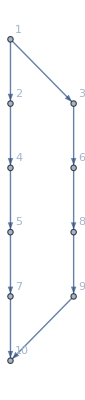

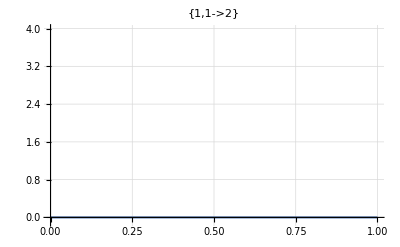
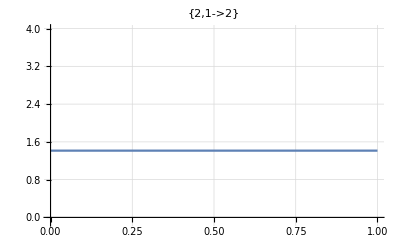
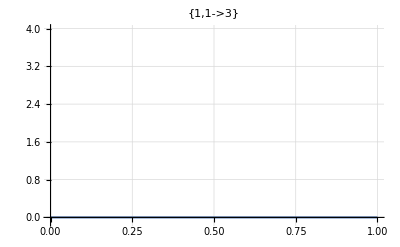
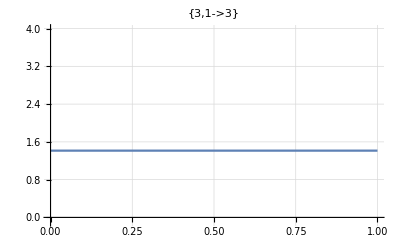
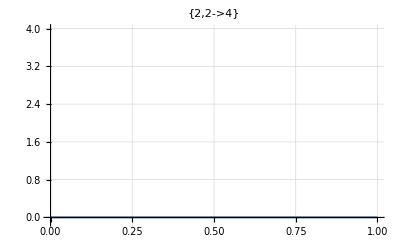
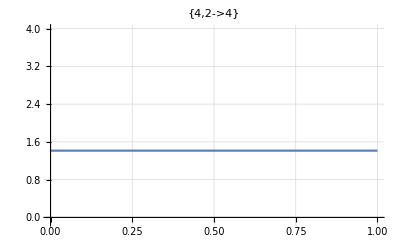
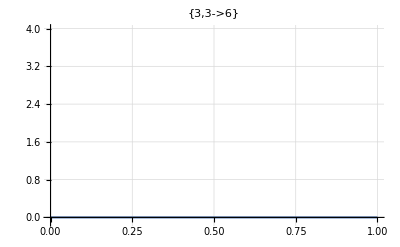

```mathematica
(*Print["jvars"];
crit["jvars"]/.crit["AssoCritical"]
Print["uvars"];
crit["uvars"]/.crit["AssoCritical"]*)
(*Don't forget to change the Range!*)
crit["BG"]

FFR=crit["AssoCritical"];
Plot[M[crit["jvars"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,4},GridLines->Automatic]&/@crit["jargs"]
Plot[U[x, #, crit,crit["AssoCritical"]],{x,0,1}, PlotLabel->#(*,PlotRange->{1-0.1,4.7}*),GridLines->Automatic]&/@crit["BEL"]
```

### Start choosing the example:

```mathematica
t="Big Braess congest";
alpha[x_]:=1;
beta = 0;
A = 0;
g[x,y]
```

x

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
Data["Entrance Vertices and Currents"]={{1,4}};
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,4}},Exit Vertices and Terminal Costs→{{9,0}},Switching Costs→{{1,3,5,10},{5,7,9,10}}|>

{0.115452,Null}

It took 0.07967 seconds to preprocess.

Iterative DNF convertion took 0.269024 seconds to terminate.

Reducing took 0.008462 seconds to terminate.

MFGSS: Multiple solutions: 0.≤jt14≤0.4

Picked one value for the variable(s) {jt14} {0.1875} (respectively)

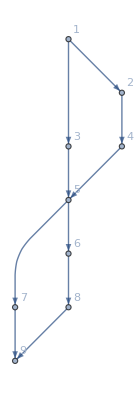

```mathematica
MFGEquations=Data2Equations[Data];//Timing
crit=CriticalCongestionSolver[MFGEquations];
crit["BG"]
```

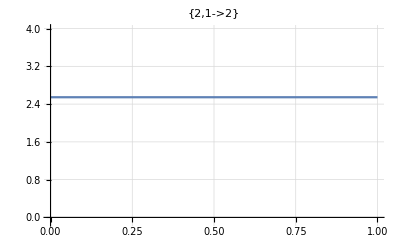
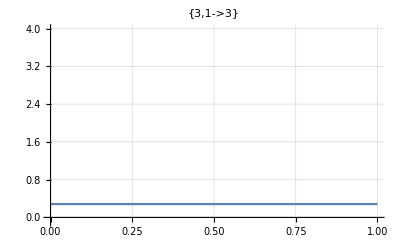
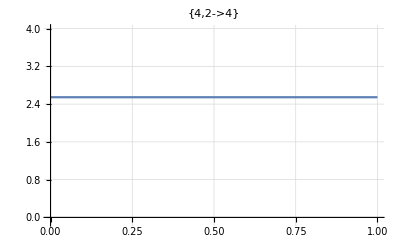
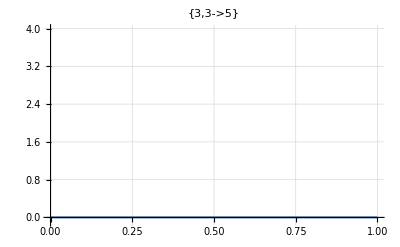
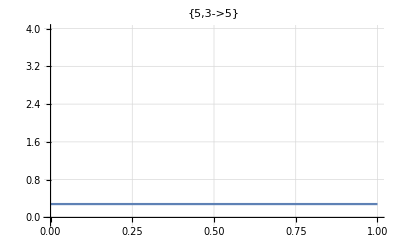
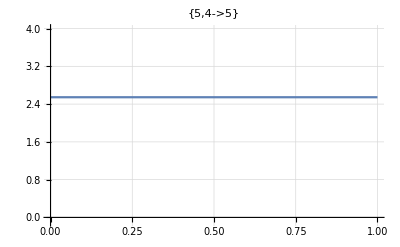
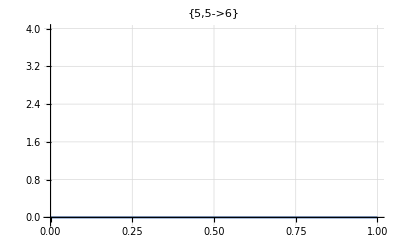
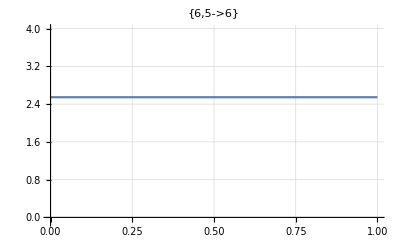
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FFR=crit["AssoCritical"];
Plot[M[crit["jvars"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,4},GridLines->Automatic]&/@crit["jargs"]
```

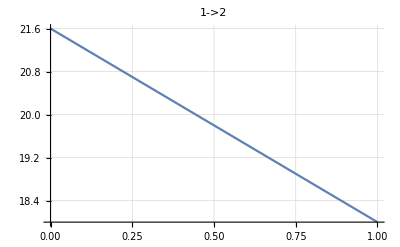
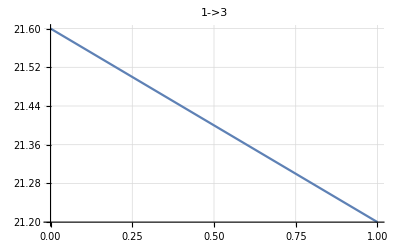
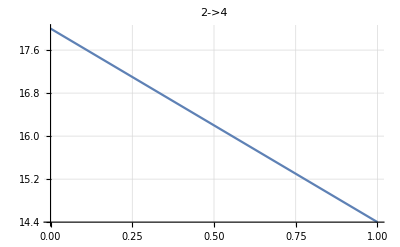
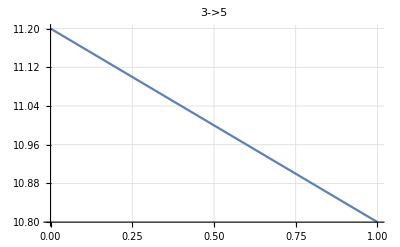
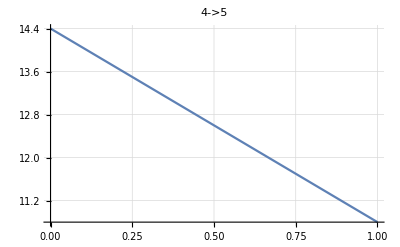
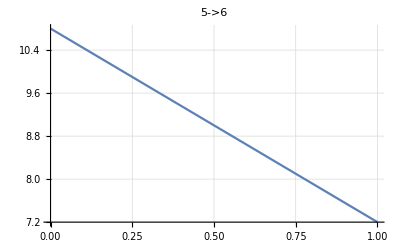
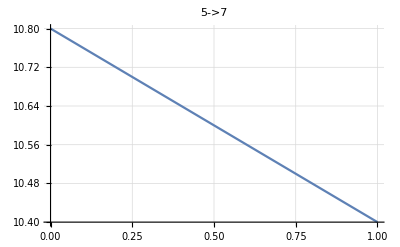
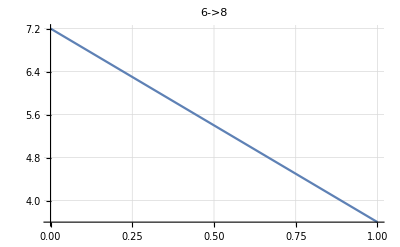

```mathematica
Plot[U[x, #, crit,FFR],{x,0,1}, PlotLabel->#(*,PlotRange->{1-0.1,4.7}*),GridLines->Automatic]&/@crit["BEL"]
```

#### Graphs for critical congestion and same hamiltonian for each edge

#### Graphs for critical congestion and different Hamiltonians on edges

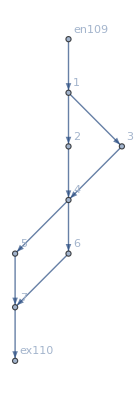

```mathematica
MFGEquations["FG"]
```

```mathematica
(*the hamiltonian that we define a posteriori needs to be consistent with the algebraic system provided by the current method.*)
```

```mathematica
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
((p+A)^2/(ϵ 2 2 m^alpha)-g[m])/.{A-> 45, ϵ-> 0.001},
edge === 1->3||edge===2->4,
((p+A)^2/(ϵ 2 2 m^alpha)-g[m])/.{A-> 1, ϵ->100},
edge === 2->3,
((p+A)^2/(ϵ 2 2 m^alpha)-g[m])/.{A-> 1, ϵ-> 0.0000001},
True,
40
]
];
```

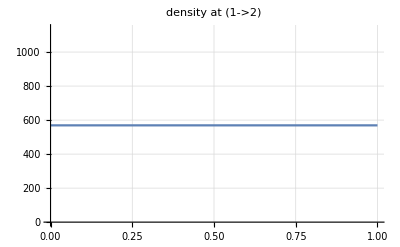
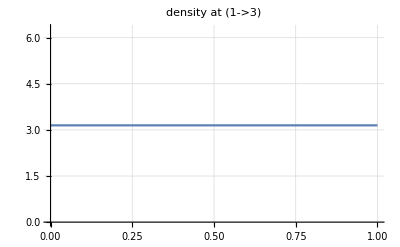
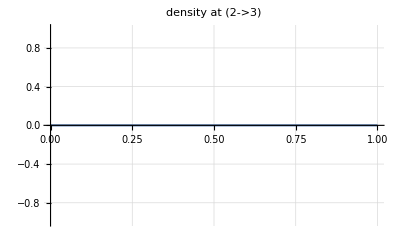
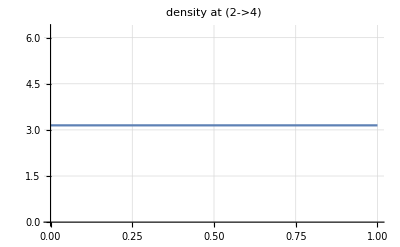
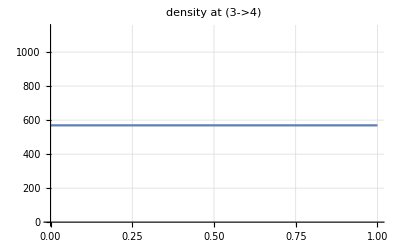

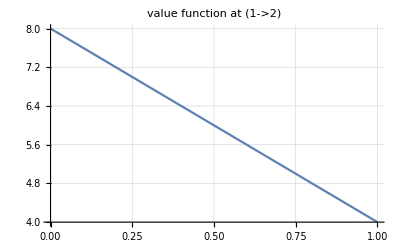
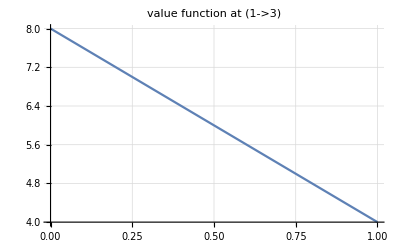
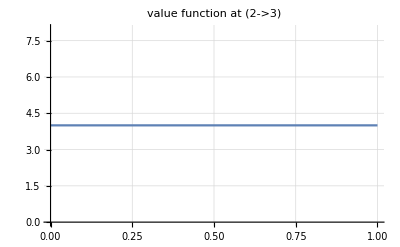

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

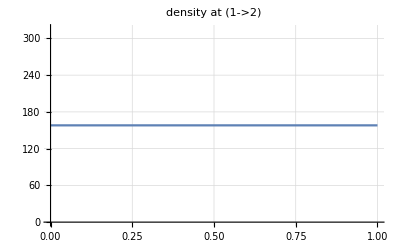
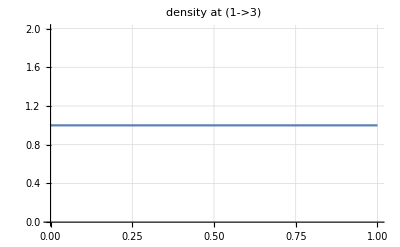
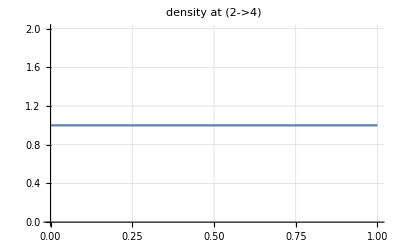
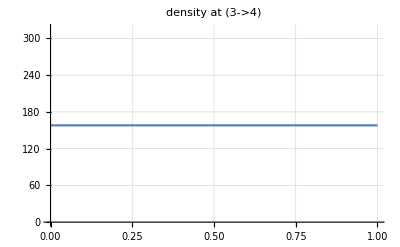
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

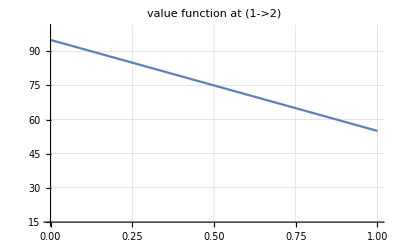
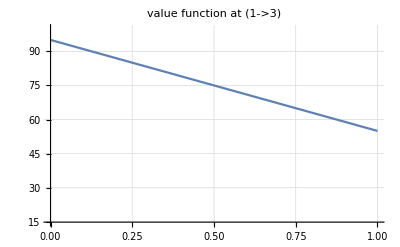
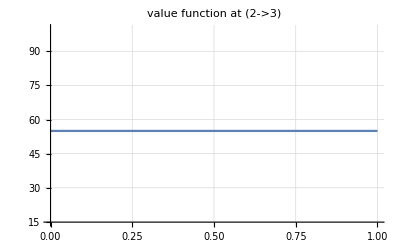
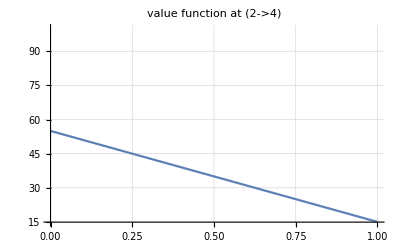
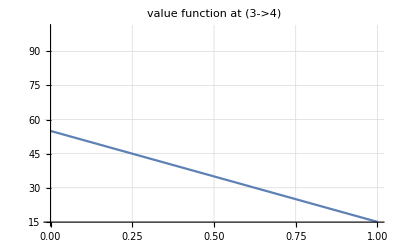

```mathematica
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m)-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m)g[m],
edge === 2->3,
p^2/(2 m)-100-m,
True,
40
]
];
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,PlotRange->{15-0.1,100},GridLines->Automatic]&/@MFGEquations["BEL"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→19.6805,u1096→19.6805,u1097→17.3402,u1098→17.3402,u1099→17.3402,u1100→15.,u1101→19.6805,u1102→17.3402,u1103→17.3402,u1104→17.3402,u1105→15.,u1106→15.,u1107→15.,u1108→19.6805|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==38.3971&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.272367

FRX1: nonlinear: 
j557-j564-u595+u602==52.7699&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0925456

FRX1: nonlinear: 
j557-j564-u595+u602==58.1516&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0334946

FRX1: nonlinear: 
j557-j564-u595+u602==60.1668&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0123877

FRX1: nonlinear: 
j557-j564-u595+u602==60.9215&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00461755

FRX1: nonlinear: 
j557-j564-u595+u602==61.2041&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00172622

FRX1: nonlinear: 
j557-j564-u595+u602==61.3099&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000646026

FRX1: nonlinear: 
j557-j564-u595+u602==61.3496&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000241869

FRX1: nonlinear: 
j557-j564-u595+u602==61.3644&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000905682

FRX1: nonlinear: 
j557-j564-u595+u602==61.37&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000339154

<|j557→63.0137,j558→16.9863,j559→15.3425,j560→47.6712,j561→32.3288,j562→80,j563→80,j564→0.,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0.,jt572→0,jt573→0,jt574→0,jt575→63.0137,jt576→16.9863,jt577→15.3425,jt578→47.6712,jt579→0.,jt580→0.,jt581→0,jt582→0,jt583→0,jt584→16.9863,jt585→0,jt586→15.3425,jt587→0,jt588→0,jt589→0,jt590→47.6712,jt591→0,jt592→32.3288,jt593→0,jt594→0,u595→64.315,u596→64.315,u597→62.6712,u598→62.6712,u599→47.3288,u600→15,u601→64.315,u602→62.6712,u603→47.3288,u604→47.3288,u605→15.,u606→15.,u607→15,u608→64.315|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→23.1887,u1096→23.1887,u1097→19.0944,u1098→19.0944,u1099→19.0944,u1100→15.,u1101→23.1887,u1102→19.0944,u1103→19.0944,u1104→19.0944,u1105→15.,u1106→15.,u1107→15.,u1108→23.1887|>

<|j530→2.85699+j537,j531→2.28602+1. j538,j533→5.14301+4.16334×10^-17 j529-4.16334×10^-17 j538+j540,j534→8,j535→8,j536→-5.14301+1. j529,j539→-2.85699+4.16334×10^-17 j529+1. j532-4.16334×10^-17 j538,j541→0,j542→0,jt543→-5.14301+1. j529,jt544→0,jt545→j537,jt546→0,jt547→j529-j537,jt548→8-j529+j537,jt549→j529-jt550,jt551→-j532+j538+jt550,jt552→j532-jt550,jt553→-5.14301+1. j529+1. j532-1. j538-1. jt550,jt554→2.28602-1. j529+1. j538+1. jt550,jt555→j538-j540+jt559,jt556→2.85699+j537-1. j538+j540-jt559,jt557→j537-jt559,jt558→2.28602-j537+1. j538+jt559,jt560→j540-jt559,jt561→j540,jt562→j532-j540,jt563→-2.85699+4.16334×10^-17 j529+1. j532-4.16334×10^-17 j538,jt564→8-j532+j540,jt565→0,jt566→0,u567→4.23814-5.55112×10^-17 jt550,u568→4.23814-5.55112×10^-17 jt550,u569→2.62409-4.16334×10^-17 j529-1.11022×10^-16 j532+4.16334×10^-17 j538,u570→2.62409-4.16334×10^-17 j529-1.11022×10^-16 j532+4.16334×10^-17 j538,u571→1.61405+4.16334×10^-17 j529-1.11022×10^-16 j532-4.16334×10^-17 j538-1.11022×10^-16 jt550,u572→0,u573→4.23814-5.55112×10^-17 jt550,u574→2.62409-4.16334×10^-17 j529-1.11022×10^-16 j532+4.16334×10^-17 j538,u575→1.61405+4.16334×10^-17 j529-1.11022×10^-16 j532-4.16334×10^-17 j538-1.11022×10^-16 jt550,u576→1.61405+4.16334×10^-17 j529-1.11022×10^-16 j532-4.16334×10^-17 j538-1.11022×10^-16 jt550,u577→0.,u578→0.,u579→0,u580→4.23814-5.55112×10^-17 jt550|>

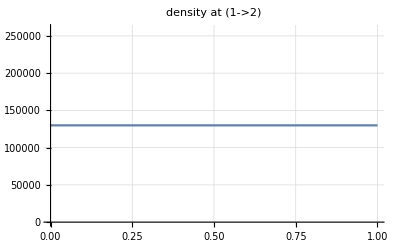
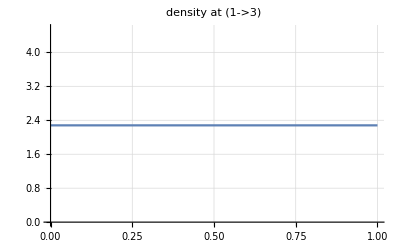
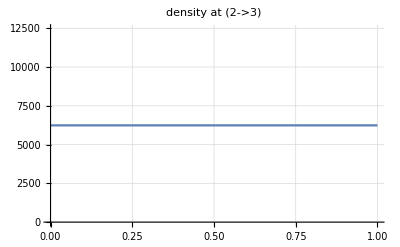
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
alpha = 0.9;
(*H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m^alpha)-20-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m^alpha)+20-g[m],
edge === 2->3,
p^2/(2 m^alpha)+20-g[m],
True,
40
]
];*)
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j883-j890-u921+u928==0.574963&&j884-j891-u922+u929==0.574963&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.574963&&j887-j894-u925+u932==0.574963

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.72378×10^-16

FRX1: nonlinear: 
j883-j890-u921+u928==0.574963&&j884-j891-u922+u929==0.574963&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.574963&&j887-j894-u925+u932==0.574963

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.72378×10^-16

<|j883→4.,j884→4.,j885→0.,j886→4.,j887→4.,j888→8,j889→8,j890→0.,j891→0,j892→0,j893→0,j894→0,j895→0,j896→0,jt897→0.,jt898→0,jt899→0,jt900→0,jt901→4.,jt902→4.,jt903→0.,jt904→4.,jt905→0.,jt906→0.,jt907→0,jt908→0,jt909→0,jt910→4.,jt911→0,jt912→0.,jt913→0,jt914→0,jt915→0,jt916→4.,jt917→0,jt918→4.,jt919→0,jt920→0,u921→6.85007,u922→6.85007,u923→3.42504,u924→3.42504,u925→3.42504,u926→0,u927→6.85007,u928→3.42504,u929→3.42504,u930→3.42504,u931→0.,u932→0.,u933→0,u934→6.85007|>

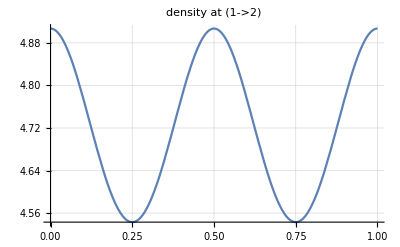
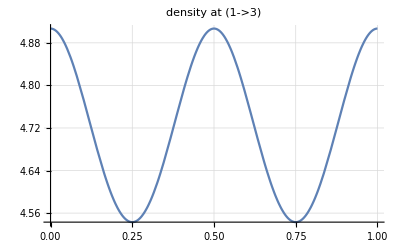
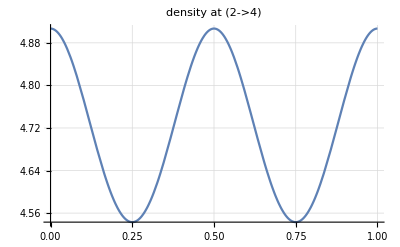
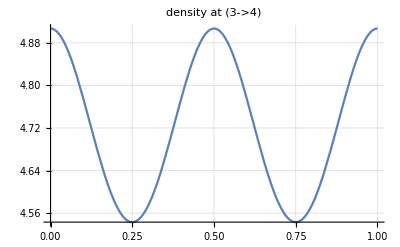
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

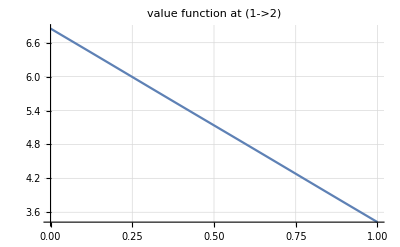
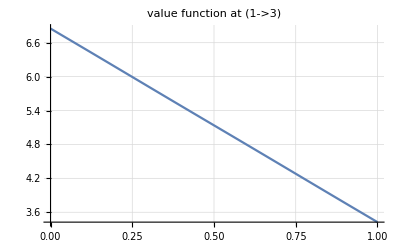
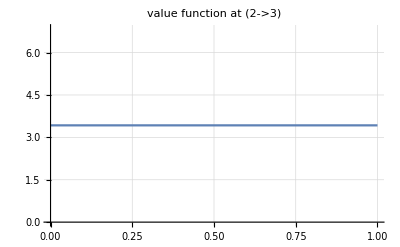
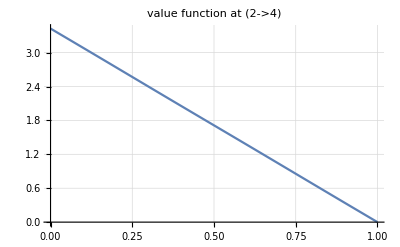
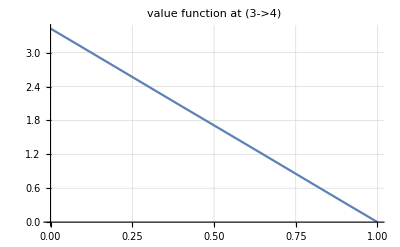

```mathematica
alpha = 0.9;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"]
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 1.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==-0.766268&&j14-j21-u52+u59==-0.766268&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-0.766268&&j17-j24-u55+u62==-0.766268

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.1591×10^-15

FRX1: nonlinear: 
j13-j20-u51+u58==-0.766268&&j14-j21-u52+u59==-0.766268&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-0.766268&&j17-j24-u55+u62==-0.766268

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.1591×10^-15

<|j13→4.,j14→4.,j15→0.,j16→4.,j17→4.,j18→8,j19→8,j20→0.,j21→0,j22→0,j23→0,j24→0,j25→0,j26→0,jt27→0.,jt28→0,jt29→0,jt30→0,jt31→4.,jt32→4.,jt33→0.,jt34→4.,jt35→0.,jt36→0.,jt37→0,jt38→0,jt39→0,jt40→4.,jt41→0,jt42→0.,jt43→0,jt44→0,jt45→0,jt46→4.,jt47→0,jt48→4.,jt49→0,jt50→0,u51→9.53254,u52→9.53254,u53→4.76627,u54→4.76627,u55→4.76627,u56→0,u57→9.53254,u58→4.76627,u59→4.76627,u60→4.76627,u61→0.,u62→0.,u63→0,u64→9.53254|>

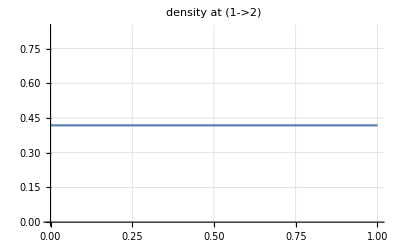
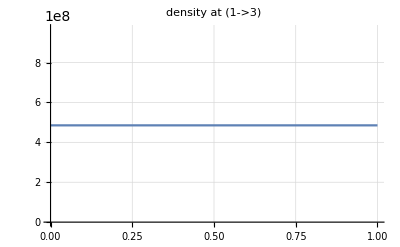
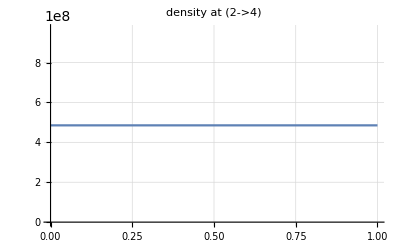
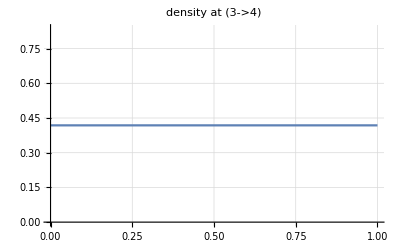
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==0.774623&&j14-j21-u52+u59==-214.393&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-214.393&&j17-j24-u55+u62==0.774623

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.02474

FRX1: nonlinear: 
j13-j20-u51+u58==-107.032&&j14-j21-u52+u59==2668.83&&j15-j22-u53+u60==-5767.05&&j16-j23-u54+u61==2668.83&&j17-j24-u55+u62==-107.032

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.02182

FRX1: nonlinear: 
j13-j20-u51+u58==32170.1&&j14-j21-u52+u59==-119858.&&j15-j22-u53+u60==259912.&&j16-j23-u54+u61==-119858.&&j17-j24-u55+u62==32170.1

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00553

FRX1: nonlinear: 
j13-j20-u51+u58==-1.07327×10^7&&j14-j21-u52+u59==1.78091×10^7&&j15-j22-u53+u60==-4.77028×10^7&&j16-j23-u54+u61==1.78091×10^7&&j17-j24-u55+u62==-1.07327×10^7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.0005

FRX1: nonlinear: 
j13-j20-u51+u58==2.55609×10^10&&j14-j21-u52+u59==-3.42117×10^10&&j15-j22-u53+u60==9.46555×10^10&&j16-j23-u54+u61==-3.42117×10^10&&j17-j24-u55+u62==2.55609×10^10

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

$Aborted

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==2.25524&&j14-j21-u52+u59==-88117.9&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-88117.9&&j17-j24-u55+u62==2.25524

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: nonlinear: 
j13-j20-u51+u58==-1.05371×10^11&&j14-j21-u52+u59==3.98128×10^11&&j15-j22-u53+u60==-2.69661×10^12&&j16-j23-u54+u61==3.98128×10^11&&j17-j24-u55+u62==-1.05371×10^11

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: nonlinear: 
j13-j20-u51+u58==2.15706×10^33&&j14-j21-u52+u59==-3.2207×10^33&&j15-j22-u53+u60==2.49175×10^34&&j16-j23-u54+u61==-3.2207×10^33&&j17-j24-u55+u62==2.15706×10^33

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

$Aborted

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==-346.136&&j14-j21-u52+u59==-346.136&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-346.136&&j17-j24-u55+u62==-346.136

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j13-j20-u51+u58==-346.136&&j14-j21-u52+u59==-346.136&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-346.136&&j17-j24-u55+u62==-346.136

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→4.,j14→4.,j15→0.,j16→4.,j17→4.,j18→8,j19→8,j20→0.,j21→0,j22→0,j23→0,j24→0,j25→0,j26→0,jt27→0.,jt28→0,jt29→0,jt30→0,jt31→4.,jt32→4.,jt33→0.,jt34→4.,jt35→0.,jt36→0.,jt37→0,jt38→0,jt39→0,jt40→4.,jt41→0,jt42→0.,jt43→0,jt44→0,jt45→0,jt46→4.,jt47→0,jt48→4.,jt49→0,jt50→0,u51→700.271,u52→700.271,u53→350.136,u54→350.136,u55→350.136,u56→0,u57→700.271,u58→350.136,u59→350.136,u60→350.136,u61→0.,u62→0.,u63→0,u64→700.271|>

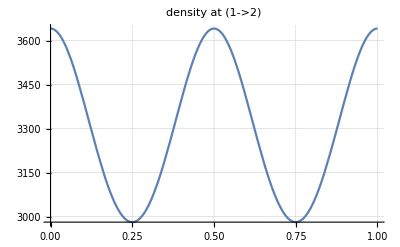
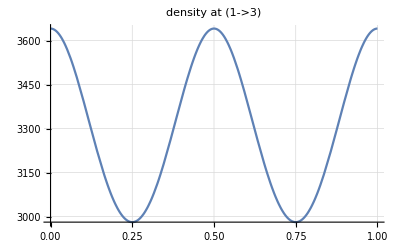
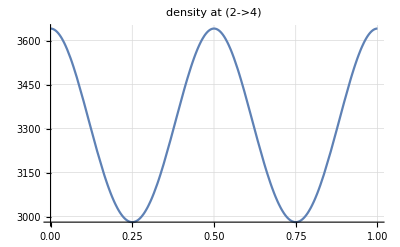
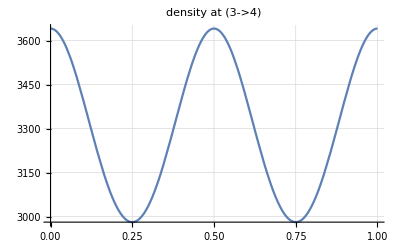
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

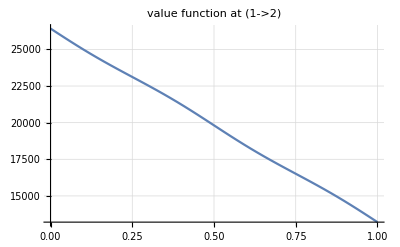
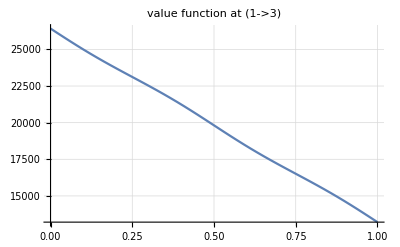
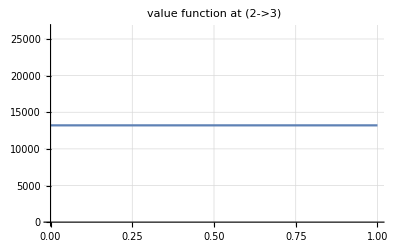
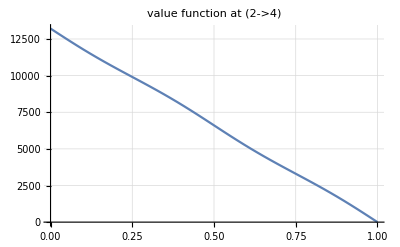
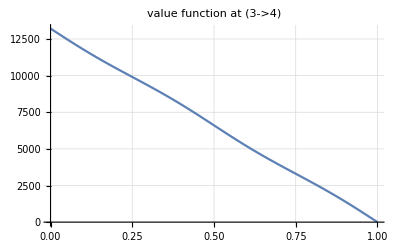

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==-13206.8&&j14-j21-u52+u59==-13206.8&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-13206.8&&j17-j24-u55+u62==-13206.8

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j13-j20-u51+u58==-13206.8&&j14-j21-u52+u59==-13206.8&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-13206.8&&j17-j24-u55+u62==-13206.8

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→4.,j14→4.,j15→0.,j16→4.,j17→4.,j18→8,j19→8,j20→0.,j21→0,j22→0,j23→0,j24→0,j25→0,j26→0,jt27→0.,jt28→0,jt29→0,jt30→0,jt31→4.,jt32→4.,jt33→0.,jt34→4.,jt35→0.,jt36→0.,jt37→0,jt38→0,jt39→0,jt40→4.,jt41→0,jt42→0.,jt43→0,jt44→0,jt45→0,jt46→4.,jt47→0,jt48→4.,jt49→0,jt50→0,u51→26421.7,u52→26421.7,u53→13210.8,u54→13210.8,u55→13210.8,u56→0,u57→26421.7,u58→13210.8,u59→13210.8,u60→13210.8,u61→0.,u62→0.,u63→0,u64→26421.7|>

## Switching costs

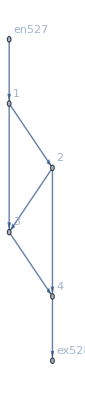

```mathematica
MFGEquations["FG"]
```

```mathematica
Data=<|"Vertices List"->{1,2,3,4},"Adjacency Matrix"->{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{4,U1}},"Switching Costs"->{{1,2,3,S1},{1,2,4,S2},{1,3,2,S3},{1,3,4,S4}}|>
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{1,3,2,S3},{1,3,4,S4}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->8,U1->0,S1->0,S2->0,S3->0,S4->0}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.125985 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.199069,Null}

```mathematica
MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]
```

<|{1,1->2,1->3}→0,{1,1->2,en1263->1}→0,{1,1->3,1->2}→0,{1,1->3,en1263->1}→0,{1,en1263->1,1->2}→4,{1,en1263->1,1->3}→4,{2,1->2,2->3}→0,{2,1->2,2->4}→4,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,1->3,2->3}→0,{3,1->3,3->4}→4,{3,2->3,1->3}→0,{3,2->3,3->4}→0,{3,3->4,1->3}→0,{3,3->4,2->3}→0,{4,2->4,3->4}→0,{4,2->4,4->ex1264}→4,{4,3->4,2->4}→0,{4,3->4,4->ex1264}→4,{4,4->ex1264,2->4}→0,{4,4->ex1264,3->4}→0|>

```mathematica
H[x,p,m,1->2]
```

```mathematica
H[x,p,m,1->3]
```

p^2/(4 m^0.1)-Log[m]

```mathematica
H
```

Function[{x,p,m,edge},Which[edge===1->2||edge===3->4,(p+A)^2/(ϵ 2 2 m^alpha)-g[m]/.{A→45,ϵ→0.001},edge===1->3||edge===2->4,(p+A)^2/(ϵ 2 2 m^alpha)-g[m]/.{A→0,ϵ→1},edge===2->3,(p+A)^2/(ϵ 2 2 m^alpha)-g[m]/.{A→0,ϵ→0.00001},True,40]]

```mathematica
alpha = .1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-0.932014+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286]^2+Abs[0.373679+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[44.5256-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-0.474387-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[-1.42316+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2),√(Abs[(-0.932014+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286)/(√(Abs[2.10245+1.11022×10^-16 j1268]^2+Abs[-4.44089×10^-16+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[2.10245+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[4.-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[4.+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(0.373679+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286)/(√(Abs[2.10245+1.11022×10^-16 j1268]^2+Abs[-4.44089×10^-16+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[2.10245+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[4.-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[4.+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(44.5256-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286)/(√(Abs[2.10245+1.11022×10^-16 j1268]^2+Abs[-4.44089×10^-16+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[2.10245+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[4.-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[4.+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-0.474387-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4])/(√(Abs[2.10245+1.11022×10^-16 j1268]^2+Abs[-4.44089×10^-16+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[2.10245+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[4.-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[4.+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-1.42316+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4])/(√(Abs[2.10245+1.11022×10^-16 j1268]^2+Abs[-4.44089×10^-16+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[2.10245+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[4.-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[4.+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2),√(Abs[(-0.932014+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286)/(√(1646.18+Abs[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(0.373679+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286)/(√(1646.18+Abs[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(44.5256-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286)/(√(1646.18+Abs[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-0.474387-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4])/(√(1646.18+Abs[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-1.42316+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4])/(√(1646.18+Abs[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[4.47439+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[3.52561-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2)]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.95337

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-1.46674+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286]^2+Abs[0.692258+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-0.733475-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-0.733475-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[-2.17534+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2),√(Abs[(-1.46674+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286)/(√(Abs[11.4218+1.11022×10^-16 j1268]^2+Abs[-20.6361+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[11.4218+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-6.33058-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-6.33058+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(0.692258+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286)/(√(Abs[11.4218+1.11022×10^-16 j1268]^2+Abs[-20.6361+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[11.4218+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-6.33058-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-6.33058+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-0.733475-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286)/(√(Abs[11.4218+1.11022×10^-16 j1268]^2+Abs[-20.6361+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[11.4218+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-6.33058-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-6.33058+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-0.733475-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4])/(√(Abs[11.4218+1.11022×10^-16 j1268]^2+Abs[-20.6361+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[11.4218+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-6.33058-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-6.33058+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-2.17534+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4])/(√(Abs[11.4218+1.11022×10^-16 j1268]^2+Abs[-20.6361+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[11.4218+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-6.33058-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-6.33058+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2),√(Abs[(-1.46674+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286)/(√(513.914+Abs[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(0.692258+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286)/(√(513.914+Abs[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-0.733475-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286)/(√(513.914+Abs[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-0.733475-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4])/(√(513.914+Abs[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-2.17534+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4])/(√(513.914+Abs[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-5.59711+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[13.5971-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2)]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-1.44601+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286]^2+Abs[0.68021+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-0.723117-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-0.723117-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[-2.14448+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2),√(Abs[(-1.44601+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286)/(√(Abs[10.7295+1.11022×10^-16 j1268]^2+Abs[-19.1693+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[10.7295+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-5.59711-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-5.59711+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(0.68021+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286)/(√(Abs[10.7295+1.11022×10^-16 j1268]^2+Abs[-19.1693+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[10.7295+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-5.59711-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-5.59711+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-0.723117-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286)/(√(Abs[10.7295+1.11022×10^-16 j1268]^2+Abs[-19.1693+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[10.7295+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-5.59711-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-5.59711+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-0.723117-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4])/(√(Abs[10.7295+1.11022×10^-16 j1268]^2+Abs[-19.1693+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[10.7295+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-5.59711-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-5.59711+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2+Abs[(-2.14448+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4])/(√(Abs[10.7295+1.11022×10^-16 j1268]^2+Abs[-19.1693+8.32667×10^-17 j1265-1.11022×10^-16 jt1286]^2+Abs[10.7295+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286]^2+Abs[-5.59711-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286]^2+Abs[-5.59711+1.11022×10^-16 j1268+1.11022×10^-16 jt1286]^2))]^2),√(Abs[(-1.44601+8.32667×10^-17 j1265-8.32667×10^-17 j1274-1.11022×10^-16 jt1286)/(√(438.861+Abs[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(0.68021+4.16334×10^-17 j1265-1.11022×10^-16 j1268-4.16334×10^-17 j1274-5.55112×10^-17 jt1286)/(√(438.861+Abs[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-0.723117-4.16334×10^-17 j1265-1.11022×10^-16 j1268+4.16334×10^-17 j1274+5.55112×10^-17 jt1286)/(√(438.861+Abs[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-0.723117-4.16334×10^-17 j1265+1.11022×10^-16 j1268+4.16334×10^-17 j1274+1.11022×10^-16 jt1286-IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4])/(√(438.861+Abs[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2+Abs[(-2.14448+4.16334×10^-17 j1265+1.11022×10^-16 j1268-4.16334×10^-17 j1274-IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4])/(√(438.861+Abs[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274+IntM[-4.87399+4.16334×10^-17 j1265-4.16334×10^-17 j1274,3->4]]^2+Abs[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274+IntM[12.874-4.16334×10^-17 j1265+4.16334×10^-17 j1274,2->4]]^2))]^2)]

FRX1: The last system in the iteration was inconsistent.
Returning the last feasible solution.

FRX1: The last system in the iteration was inconsistent.
Returning the last feasible solution.

FRX1: The last system in the iteration was inconsistent.
Returning the last feasible solution.

$Aborted

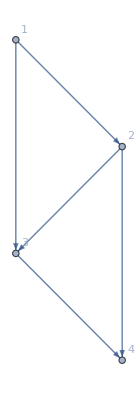
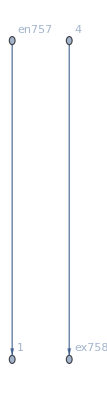
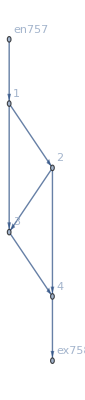
<|BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en757|>,InEdges→{en757->1},ExitVertices→{4},OutwardVertices→<|4→ex758|>,OutEdges→{4->ex758},AuxiliaryGraph→-Graphics-,FG→-Graphics-,VL→{1,2,3,4},EL→{1->2,1->3,2->3,2->4,3->4,4->ex758,en757->1},BEL→{1->2,1->3,2->3,2->4,3->4},FVL→{1,2,3,4,en757,ex758},AllTransitions→{{1,1->2,1->3},{1,1->2,en757->1},{1,1->3,1->2},{1,1->3,en757->1},{1,en757->1,1->2},{1,en757->1,1->3},{2,1->2,2->3},{2,1->2,2->4},{2,2->3,1->2},{2,2->3,2->4},{2,2->4,1->2},{2,2->4,2->3},{3,1->3,2->3},{3,1->3,3->4},{3,2->3,1->3},{3,2->3,3->4},{3,3->4,1->3},{3,3->4,2->3},{4,2->4,3->4},{4,2->4,4->ex758},{4,3->4,2->4},{4,3->4,4->ex758},{4,4->ex758,2->4},{4,4->ex758,3->4}},NoDeadEnds→{{1,1->2},{1,1->3},{1,en757->1},{2,1->2},{2,2->3},{2,2->4},{3,1->3},{3,2->3},{3,3->4},{4,2->4},{4,3->4},{4,4->ex758}},NoDeadStarts→{{2,1->2},{3,1->3},{en757,en757->1},{1,1->2},{3,2->3},{4,2->4},{1,1->3},{2,2->3},{4,3->4},{2,2->4},{3,3->4},{ex758,4->ex758}},jargs→{{2,1->2},{3,1->3},{3,2->3},{4,2->4},{4,3->4},{ex758,4->ex758},{1,en757->1},{1,1->2},{1,1->3},{2,2->3},{2,2->4},{3,3->4},{4,4->ex758},{en757,en757->1}},js→{j759,j760,j761,j762,j763,j764,j765,j766,j767,j768,j769,j770,j771,j772},jvars→<|{2,1->2}→j759,{3,1->3}→j760,{3,2->3}→j761,{4,2->4}→j762,{4,3->4}→j763,{ex758,4->ex758}→j764,{1,en757->1}→j765,{1,1->2}→j766,{1,1->3}→j767,{2,2->3}→j768,{2,2->4}→j769,{3,3->4}→j770,{4,4->ex758}→j771,{en757,en757->1}→j772|>,jts→{jt773,jt774,jt775,jt776,jt777,jt778,jt779,jt780,jt781,jt782,jt783,jt784,jt785,jt786,jt787,jt788,jt789,jt790,jt791,jt792,jt793,jt794,jt795,jt796},jtvars→<|{1,1->2,1->3}→jt773,{1,1->2,en757->1}→jt774,{1,1->3,1->2}→jt775,{1,1->3,en757->1}→jt776,{1,en757->1,1->2}→jt777,{1,en757->1,1->3}→jt778,{2,1->2,2->3}→jt779,{2,1->2,2->4}→jt780,{2,2->3,1->2}→jt781,{2,2->3,2->4}→jt782,{2,2->4,1->2}→jt783,{2,2->4,2->3}→jt784,{3,1->3,2->3}→jt785,{3,1->3,3->4}→jt786,{3,2->3,1->3}→jt787,{3,2->3,3->4}→jt788,{3,3->4,1->3}→jt789,{3,3->4,2->3}→jt790,{4,2->4,3->4}→jt791,{4,2->4,4->ex758}→jt792,{4,3->4,2->4}→jt793,{4,3->4,4->ex758}→jt794,{4,4->ex758,2->4}→jt795,{4,4->ex758,3->4}→jt796|>,uargs→{{1,1->2},{1,1->3},{2,2->3},{2,2->4},{3,3->4},{4,4->ex758},{en757,en757->1},{2,1->2},{3,1->3},{3,2->3},{4,2->4},{4,3->4},{ex758,4->ex758},{1,en757->1}},us→{u797,u798,u799,u800,u801,u802,u803,u804,u805,u806,u807,u808,u809,u810},uvars→<|{1,1->2}→u797,{1,1->3}→u798,{2,2->3}→u799,{2,2->4}→u800,{3,3->4}→u801,{4,4->ex758}→u802,{en757,en757->1}→u803,{2,1->2}→u804,{3,1->3}→u805,{3,2->3}→u806,{4,2->4}→u807,{4,3->4}→u808,{ex758,4->ex758}→u809,{1,en757->1}→u810|>,SwitchingCosts→<|{1,1->2,1->3}→0,{1,1->2,en757->1}→∞,{1,1->3,1->2}→0,{1,1->3,en757->1}→∞,{1,en757->1,1->2}→0,{1,en757->1,1->3}→0,{2,1->2,2->3}→0,{2,1->2,2->4}→3,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,1->3,2->3}→0,{3,1->3,3->4}→0,{3,2->3,1->3}→0,{3,2->3,3->4}→0,{3,3->4,1->3}→0,{3,3->4,2->3}→0,{4,2->4,3->4}→0,{4,2->4,4->ex758}→0,{4,3->4,2->4}→0,{4,3->4,4->ex758}→0,{4,4->ex758,2->4}→∞,{4,4->ex758,3->4}→∞,{4,4->ex758,1->2}→∞,{4,4->ex758,1->3}→∞,{4,4->ex758,2->3}→∞,{4,4->ex758,4->ex758}→∞,{4,4->ex758,en757->1}→∞,{1,en757->1,en757->1}→∞|>,OutRules→{{4,4->ex758,1->2}→∞,{4,4->ex758,1->3}→∞,{4,4->ex758,2->3}→∞,{4,4->ex758,2->4}→∞,{4,4->ex758,3->4}→∞,{4,4->ex758,4->ex758}→∞,{4,4->ex758,en757->1}→∞},InRules→{{1,1->2,en757->1}→∞,{1,1->3,en757->1}→∞,{1,en757->1,en757->1}→∞},EntryArgs→{{1,en757->1}},EntryDataAssociation→<|{1,en757->1}→8|>,jays→<|1->2→j759-j766,1->3→j760-j767,2->3→j761-j768,2->4→j762-j769,3->4→j763-j770|>,NonZeroEntryCurrents→True,ExitCosts→<|ex758→0|>,EqCurrentCompCon→(j766==0||j759==0)&&(j767==0||j760==0)&&(j768==0||j761==0)&&(j769==0||j762==0)&&(j770==0||j763==0)&&(j771==0||j764==0)&&(j772==0||j765==0),EqTransitionCompCon→(jt773==0||jt775==0)&&(jt774==0||jt777==0)&&(jt776==0||jt778==0)&&(jt779==0||jt781==0)&&(jt780==0||jt783==0)&&(jt782==0||jt784==0)&&(jt785==0||jt787==0)&&(jt786==0||jt789==0)&&(jt788==0||jt790==0)&&(jt791==0||jt793==0)&&(jt792==0||jt795==0)&&(jt794==0||jt796==0),EqCompCon→(jt773==0||-u797+u798==0)&&jt774==0&&(jt775==0||u797-u798==0)&&jt776==0&&(jt777==0||u797-u810==0)&&(jt778==0||u798-u810==0)&&(jt779==0||u799-u804==0)&&(jt780==0||3+u800-u804==0)&&(jt781==0||-u799+u804==0)&&(jt782==0||-u799+u800==0)&&(jt783==0||-u800+u804==0)&&(jt784==0||u799-u800==0)&&(jt785==0||-u805+u806==0)&&(jt786==0||u801-u805==0)&&(jt787==0||u805-u806==0)&&(jt788==0||u801-u806==0)&&(jt789==0||-u801+u805==0)&&(jt790==0||-u801+u806==0)&&(jt791==0||-u807+u808==0)&&(jt792==0||u802-u807==0)&&(jt793==0||u807-u808==0)&&(jt794==0||u802-u808==0)&&jt795==0&&jt796==0,EqAllComp→(j766==0||j759==0)&&(j767==0||j760==0)&&(j768==0||j761==0)&&(j769==0||j762==0)&&(j770==0||j763==0)&&(j771==0||j764==0)&&(j772==0||j765==0)&&(jt773==0||jt775==0)&&(jt774==0||jt777==0)&&(jt776==0||jt778==0)&&(jt779==0||jt781==0)&&(jt780==0||jt783==0)&&(jt782==0||jt784==0)&&(jt785==0||jt787==0)&&(jt786==0||jt789==0)&&(jt788==0||jt790==0)&&(jt791==0||jt793==0)&&(jt792==0||jt795==0)&&(jt794==0||jt796==0)&&(jt773==0||-u797+u798==0)&&jt774==0&&(jt775==0||u797-u798==0)&&jt776==0&&(jt777==0||u797-u810==0)&&(jt778==0||u798-u810==0)&&(jt779==0||u799-u804==0)&&(jt780==0||3+u800-u804==0)&&(jt781==0||-u799+u804==0)&&(jt782==0||-u799+u800==0)&&(jt783==0||-u800+u804==0)&&(jt784==0||u799-u800==0)&&(jt785==0||-u805+u806==0)&&(jt786==0||u801-u805==0)&&(jt787==0||u805-u806==0)&&(jt788==0||u801-u806==0)&&(jt789==0||-u801+u805==0)&&(jt790==0||-u801+u806==0)&&(jt791==0||-u807+u808==0)&&(jt792==0||u802-u807==0)&&(jt793==0||u807-u808==0)&&(jt794==0||u802-u808==0)&&jt795==0&&jt796==0,EqPosCon→NonNegative[j759]&&NonNegative[j760]&&NonNegative[j761]&&NonNegative[j762]&&NonNegative[j763]&&NonNegative[j764]&&NonNegative[j765]&&NonNegative[j766]&&NonNegative[j767]&&NonNegative[j768]&&NonNegative[j769]&&NonNegative[j770]&&NonNegative[j771]&&NonNegative[j772]&&NonNegative[jt773]&&NonNegative[jt774]&&NonNegative[jt775]&&NonNegative[jt776]&&NonNegative[jt777]&&NonNegative[jt778]&&NonNegative[jt779]&&NonNegative[jt780]&&NonNegative[jt781]&&NonNegative[jt782]&&NonNegative[jt783]&&NonNegative[jt784]&&NonNegative[jt785]&&NonNegative[jt786]&&NonNegative[jt787]&&NonNegative[jt788]&&NonNegative[jt789]&&NonNegative[jt790]&&NonNegative[jt791]&&NonNegative[jt792]&&NonNegative[jt793]&&NonNegative[jt794]&&NonNegative[jt795]&&NonNegative[jt796],EqBalanceSplittingCurrents→j766==jt773+jt774&&j767==jt775+jt776&&j765==jt777+jt778&&j759==jt779+jt780&&j768==jt781+jt782&&j769==jt783+jt784&&j760==jt785+jt786&&j761==jt787+jt788&&j770==jt789+jt790&&j762==jt791+jt792&&j763==jt793+jt794&&j771==jt795+jt796,EqBalanceGatheringCurrents→j759==jt775+jt777&&j760==jt773+jt778&&j772==jt774+jt776&&j766==jt781+jt783&&j761==jt779+jt784&&j762==jt780+jt782&&j767==jt787+jt789&&j768==jt785+jt790&&j763==jt786+jt788&&j769==jt793+jt795&&j770==jt791+jt796&&j764==jt792+jt794,EqEntryIn→j765==8,EqExitValues→u809==0,EqSwitchingConditions→u798≥u810&&u797==u798&&u799==u804&&u800==u799&&u805==u806&&u801==u805&&u802≥u808&&u807==u808,EqValueAuxiliaryEdges→-u803+u810==0&&-u802+u809==0,EqAll→NonNegative[j759]&&NonNegative[j760]&&NonNegative[j761]&&NonNegative[j762]&&NonNegative[j763]&&NonNegative[j764]&&NonNegative[j765]&&NonNegative[j766]&&NonNegative[j767]&&NonNegative[j768]&&NonNegative[j769]&&NonNegative[j770]&&NonNegative[j771]&&NonNegative[j772]&&NonNegative[jt773]&&NonNegative[jt774]&&NonNegative[jt775]&&NonNegative[jt776]&&NonNegative[jt777]&&NonNegative[jt778]&&NonNegative[jt779]&&NonNegative[jt780]&&NonNegative[jt781]&&NonNegative[jt782]&&NonNegative[jt783]&&NonNegative[jt784]&&NonNegative[jt785]&&NonNegative[jt786]&&NonNegative[jt787]&&NonNegative[jt788]&&NonNegative[jt789]&&NonNegative[jt790]&&NonNegative[jt791]&&NonNegative[jt792]&&NonNegative[jt793]&&NonNegative[jt794]&&NonNegative[jt795]&&NonNegative[jt796]&&j766==jt773+jt774&&j767==jt775+jt776&&j765==jt777+jt778&&j759==jt779+jt780&&j768==jt781+jt782&&j769==jt783+jt784&&j760==jt785+jt786&&j761==jt787+jt788&&j770==jt789+jt790&&j762==jt791+jt792&&j763==jt793+jt794&&j771==jt795+jt796&&j759==jt775+jt777&&j760==jt773+jt778&&j772==jt774+jt776&&j766==jt781+jt783&&j761==jt779+jt784&&j762==jt780+jt782&&j767==jt787+jt789&&j768==jt785+jt790&&j763==jt786+jt788&&j769==jt793+jt795&&j770==jt791+jt796&&j764==jt792+jt794&&j765==8&&u809==0&&u798≥u810&&u797==u798&&u799==u804&&u800==u799&&u805==u806&&u801==u805&&u802≥u808&&u807==u808&&-u803+u810==0&&-u802+u809==0,EqAllAll→NonNegative[j759]&&NonNegative[j760]&&NonNegative[j761]&&NonNegative[j762]&&NonNegative[j763]&&NonNegative[j764]&&NonNegative[j765]&&NonNegative[j766]&&NonNegative[j767]&&NonNegative[j768]&&NonNegative[j769]&&NonNegative[j770]&&NonNegative[j771]&&NonNegative[j772]&&NonNegative[jt773]&&NonNegative[jt774]&&NonNegative[jt775]&&NonNegative[jt776]&&NonNegative[jt777]&&NonNegative[jt778]&&NonNegative[jt779]&&NonNegative[jt780]&&NonNegative[jt781]&&NonNegative[jt782]&&NonNegative[jt783]&&NonNegative[jt784]&&NonNegative[jt785]&&NonNegative[jt786]&&NonNegative[jt787]&&NonNegative[jt788]&&NonNegative[jt789]&&NonNegative[jt790]&&NonNegative[jt791]&&NonNegative[jt792]&&NonNegative[jt793]&&NonNegative[jt794]&&NonNegative[jt795]&&NonNegative[jt796]&&j766==jt773+jt774&&j767==jt775+jt776&&j765==jt777+jt778&&j759==jt779+jt780&&j768==jt781+jt782&&j769==jt783+jt784&&j760==jt785+jt786&&j761==jt787+jt788&&j770==jt789+jt790&&j762==jt791+jt792&&j763==jt793+jt794&&j771==jt795+jt796&&j759==jt775+jt777&&j760==jt773+jt778&&j772==jt774+jt776&&j766==jt781+jt783&&j761==jt779+jt784&&j762==jt780+jt782&&j767==jt787+jt789&&j768==jt785+jt790&&j763==jt786+jt788&&j769==jt793+jt795&&j770==jt791+jt796&&j764==jt792+jt794&&j765==8&&u809==0&&u798≥u810&&u797==u798&&u799==u804&&u800==u799&&u805==u806&&u801==u805&&u802≥u808&&u807==u808&&-u803+u810==0&&-u802+u809==0&&(j766==0||j759==0)&&(j767==0||j760==0)&&(j768==0||j761==0)&&(j769==0||j762==0)&&(j770==0||j763==0)&&(j771==0||j764==0)&&(j772==0||j765==0)&&(jt773==0||jt775==0)&&(jt774==0||jt777==0)&&(jt776==0||jt778==0)&&(jt779==0||jt781==0)&&(jt780==0||jt783==0)&&(jt782==0||jt784==0)&&(jt785==0||jt787==0)&&(jt786==0||jt789==0)&&(jt788==0||jt790==0)&&(jt791==0||jt793==0)&&(jt792==0||jt795==0)&&(jt794==0||jt796==0)&&(jt773==0||-u797+u798==0)&&jt774==0&&(jt775==0||u797-u798==0)&&jt776==0&&(jt777==0||u797-u810==0)&&(jt778==0||u798-u810==0)&&(jt779==0||u799-u804==0)&&(jt780==0||3+u800-u804==0)&&(jt781==0||-u799+u804==0)&&(jt782==0||-u799+u800==0)&&(jt783==0||-u800+u804==0)&&(jt784==0||u799-u800==0)&&(jt785==0||-u805+u806==0)&&(jt786==0||u801-u805==0)&&(jt787==0||u805-u806==0)&&(jt788==0||u801-u806==0)&&(jt789==0||-u801+u805==0)&&(jt790==0||-u801+u806==0)&&(jt791==0||-u807+u808==0)&&(jt792==0||u802-u807==0)&&(jt793==0||u807-u808==0)&&(jt794==0||u802-u808==0)&&jt795==0&&jt796==0,BoundaryRules→{j765→8,u809→0},RulesEntryIn→{j765→8},RulesExitValues→{u809→0},Nlhs→{j759-j766-u797+u804,j760-j767-u798+u805,j761-j768-u799+u806,j762-j769-u800+u807,j763-j770-u801+u808},EqCriticalCase→j759-j766-u797+u804==0&&j760-j767-u798+u805==0&&j761-j768-u799+u806==0&&j762-j769-u800+u807==0&&j763-j770-u801+u808==0,criticalreduced1→{Reduce[DeleteDuplicates[False],ℝ],<|j759→4+jt773,j761→-4+j760+j763-jt786-jt789,j762→4+jt793,j764→8,j765→8,j766→jt773,j767→-4+j760,j768→-4+j760+j763-jt786-jt789,j769→jt793,j770→-4+j763,j771→0,j772→0,jt774→0,jt775→-4+j760,jt776→0,jt777→8-j760+jt773,jt778→j760-jt773,jt780→0,jt781→-8+j760+j763-jt786-jt789-jt793,jt782→4+jt793,jt783→8-j760-j763+jt773+jt786+jt789+jt793,jt784→-8+j760+j763-jt773-jt786-jt789,jt785→j760-jt786,jt787→-4+j760-jt789,jt788→j763-jt786,jt790→-4+j763-jt789,jt791→-4+j763,jt792→8-j763+jt793,jt794→j763-jt793,jt795→0,jt796→0,u797→4+u801,u798→4+u801,u799→u801,u800→u801,u802→0,u804→u801,u805→u801,u806→u801,u807→-4+u801,u808→-4+u801,u809→0,u810→u803,jt779→4+jt773|>},Nrhs→{j759-j766+IntM[j759-j766,1->2],j760-j767+IntM[j760-j767,1->3],j761-j768+IntM[j761-j768,2->3],j762-j769+IntM[j762-j769,2->4],j763-j770+IntM[j763-j770,3->4]},EqGeneralCase→j759-j766-u797+u804==j759-j766+IntM[j759-j766,1->2]&&j760-j767-u798+u805==j760-j767+IntM[j760-j767,1->3]&&j761-j768-u799+u806==j761-j768+IntM[j761-j768,2->3]&&j762-j769-u800+u807==j762-j769+IntM[j762-j769,2->4]&&j763-j770-u801+u808==j763-j770+IntM[j763-j770,3->4],TOL→1/1000000|>

```mathematica
MFGEquations
```

```mathematica
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
First@FindInstance[0≤jt2744≤8/5&&jt2743==1/5 (22-5 jt2744)&&jt2741==1/5 (8-5 jt2744)&&jt2740==jt2744,{jt2744,jt2743,jt2741,jt2740}, Reals]
```

{jt2744→27/64,jt2743→1273/320,jt2741→377/320,jt2740→27/64}

```mathematica
(Association@{jt2744->27/64,jt2743->1273/320,jt2741->377/320,jt2740->27/64})
```

```mathematica
lenga=<|jt2744->27/64,jt2743->1273/320,jt2741->377/320,jt2740->27/64|>
```

<|jt2744→27/64,jt2743→1273/320,jt2741→377/320,jt2740→27/64|>

```mathematica
Keys[lenga]
```

{jt2744,jt2743,jt2741,jt2740}

```mathematica
Values[lenga]
```

{27/64,1273/320,377/320,27/64}

```mathematica
Rule[%431,%432]
```

{jt2744,jt2743,jt2741,jt2740}→{27/64,1273/320,377/320,27/64}

```mathematica
And@@(Outer[Equal,%431,%432]//Diagonal)
```

jt2744==27/64&&jt2743==1273/320&&jt2741==377/320&&jt2740==27/64

```mathematica
ToRules[lenga]
```

ToRules[<|jt2744→27/64,jt2743→1273/320,jt2741→377/320,jt2740→27/64|>]